# Muon Production in SM - γ-> μ^- μ^+

## Load FeynArts and FormCalc

```mathematica
Quit[]
```

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

## Set-up

```mathematica
CKM=IndexDelta;
```

```mathematica
process={V[1]} -> {F[2,{2}], -F[2,{2}]};
```

```mathematica
name="A-mm-SM";
```

```mathematica
SetOptions[InsertFields,Model->"SM",GenericModel->"Lorentz",InsertionLevel->Particles];
SetOptions[Paint,PaintLevel->{Classes},ColumnsXRows->{4,5}];
```

## Tree-Level

## Topologies

> Top. 1 ad/bdcd/0.m, 0 diagrams

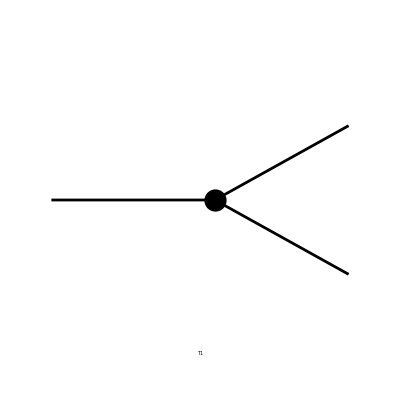

```mathematica
tops=CreateTopologies[0,1->2,Adjacencies->3];
Paint[tops];
```

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

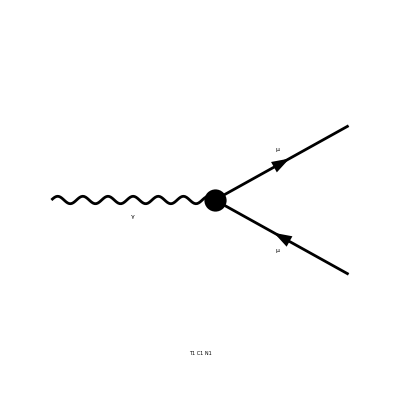

```mathematica
ins=InsertFields[tops, process];
Paint[ins];
```

## Feynman Amplitudes

```mathematica
amp=CreateFeynAmp[ins,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

## FormCalc results

```mathematica
ClearProcess[]
```

```mathematica
result=CalcFeynAmp[amp]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-EL (F1+F2)]

```mathematica
UVDivergentPart[result]
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0]

## One-Loop

## Topologies

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

> Top. 4 ad/bece/efdfdf.m, 0 diagrams

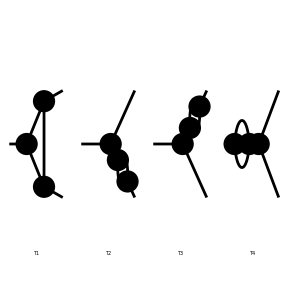

```mathematica
tops1=CreateTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->Tadpoles];
Paint[tops1];
```

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

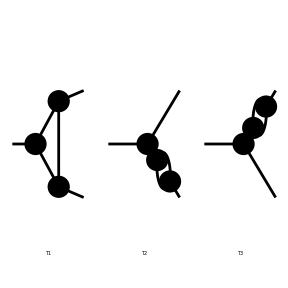

```mathematica
tops1=Delete[tops1,4];
Paint[tops1];
```

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 6 Generic, 8 Classes, 8 Particles insertions

> Top. 2: 2 Generic, 6 Classes, 6 Particles insertions

> Top. 3: 2 Generic, 6 Classes, 6 Particles insertions

in total: 10 Generic, 20 Classes, 20 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

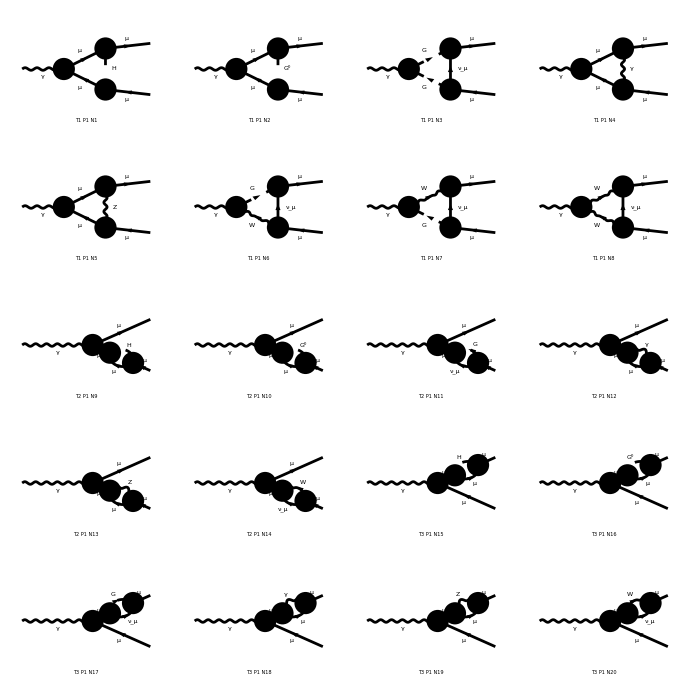

```mathematica
ins1=InsertFields[tops1, process];
Paint[ins1, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
amp1=CreateFeynAmp[ins1,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 8 Particles amplitudes

> Top. 2: 6 Particles amplitudes

> Top. 3: 6 Particles amplitudes

in total: 20 Particles amplitudes

## FormCalc results

```mathematica
result1=CalcFeynAmp[amp1/.replacement]//Simplify
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-1/(16 CW2 π SW2)Alfa EL MM (CW2 Finite Sub40 SW2+2 Sub14 SW2 B0i[bb0,MM2,MM2,MZ2]+4 CW2 Sub38 C0i[cc0,MM2,0,MM2,0,MW2,MW2]-4 (Sub14 SW2 C0i[cc00,0,MM2,MM2,MM2,MM2,MZ2]+CW2 Sub41 C0i[cc00,MM2,0,MM2,0,MW2,MW2])-4 CW2 (F3-F4) (B0i[bb0,MM2,0,MW2]-2 MM2 (C0i[cc1,MM2,0,MM2,0,MW2,MW2]+C0i[cc2,MM2,0,MM2,0,MW2,MW2])))]

```mathematica
UVDivergentPart[result1]/.Subexpr[]//Simplify
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa Divergence EL (F3-F4) MM (-CW2 MM2+MW2+6 CW2 MW2-4 MW2 SW2))/(16 CW2 MW2 π SW2)]

## Amplitude manipulations

## Amplitude manipulation tools

```mathematica
selectFeynAmp[amp_,i_Integer/;i≥0]:=amp[[0]][amp[[i]]]
```

```mathematica
calcFeynAmp[amp_,i_Integer/;i≥0]:=CalcFeynAmp[amp[[0]][amp[[i]]]]
```

```mathematica
calcFeynAmpList[amp_]:=Map[CalcFeynAmp[amp[[0]][#]]&,amp]
```

```mathematica
replacement={PolarizationVector[V[1],FourMomentum[Incoming,1],Index[Lorentz,i_Integer]]->FourVector[FourMomentum[Incoming,1],Index[Lorentz,i]]}
```

{ep[V[1],p1,Lori_Integer]→(p1)[Lori]}

## Computations

```mathematica
Length[amp1]
```

20

```mathematica
result1List=calcFeynAmpList[amp1/.replacement]/.result1List[[0]]->List;
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

```mathematica
uvDiv=Map[UVDivergentPart,result1List]//Simplify
```

{Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL (F3-F4) MM MM2)/(16 MW2 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL MM Sub14)/(16 CW2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(3 Alfa Divergence EL (F3-F4) MM)/(8 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0]}

```mathematica
uvDivL=Map[#[[1]]&,uvDiv]/.uvDivL[[0]]->List
```

{0,0,-(Alfa Divergence EL (F3-F4) MM MM2)/(16 MW2 π SW2),0,-(Alfa Divergence EL MM Sub14)/(16 CW2 π),0,0,(3 Alfa Divergence EL (F3-F4) MM)/(8 π SW2),0,0,0,0,0,0,0,0,0,0,0,0}

## Diagram Selection

## Z Boson

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

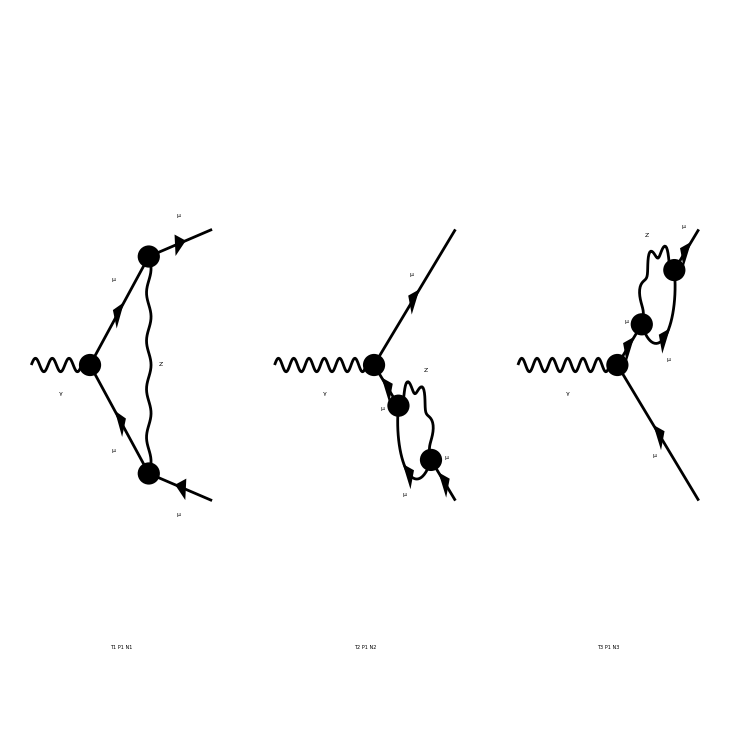

```mathematica
insZ=DiagramSelect[ins1,!FreeQ[#,V[2]]&];
Paint[insZ,PaintLevel->{Particles}];
```

```mathematica
ampZ=CreateFeynAmp[insZ,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 3 Particles amplitudes

```mathematica
resultZ=CalcFeynAmp[ampZ/.replacement]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(Alfa EL MM Sub14 (Finite/16-1/8 B0i[bb0,MM2,MM2,MZ2]+1/4 C0i[cc00,0,MM2,MM2,MM2,MM2,MZ2]))/(CW2 π)]

```mathematica
UVDivergentPart[resultZ]//Simplify
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL MM Sub14)/(16 CW2 π)]

```mathematica
resultZList=calcFeynAmpList[ampZ/.replacement]/.resultZList[[0]]->List;
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

```mathematica
uvDivZ=Map[UVDivergentPart,resultZList]//Simplify
```

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL MM Sub14)/(16 CW2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0]]

```mathematica
uvDivZL=Map[#[[1]]&,uvDivZ]/.uvDivZ[[0]]->List
```

{-(Alfa Divergence EL MM Sub14)/(16 CW2 π),0,0}

```mathematica
Subexpr[]
```

{Sub29→2 MM2+MM2^2/MW2,Sub38→(F3-F4) (MM2-MW2),Sub13→(F1+F2) MM-(F3+F4) Pair1,Sub37→(F1+3 F2) MM2-2 F3 MM Pair1,Sub31→-(F1+F2) MM2+2 F3 MM Pair1,Sub36→(F1+3 F2) MM2-2 F4 MM Pair1,Sub32→-(F1+F2) MM2+2 F4 MM Pair1,Sub35→(F1+F2) MM2-2 (F3+F4) MM Pair1,Sub1→(F1+F2) MM2-(F3+F4) MM Pair1,Sub24→(F1+F2) MM2+2 (F3+F4) MM Pair1,Sub30→(F1+F2) MM2^2-2 (F3+F4) MM MM2 Pair1,Sub26→2 F2 MM2-F3 MM (2-MM2/MW2) Pair1,Sub25→2 F2 MM2-F4 MM (2-MM2/MW2) Pair1,Sub10→(F1+F2) (Sub2+Sub3)+MM Sub8-2 MM2 Sub9,Sub12→-2 (Sub11+(F2 Sub4)/CW)+(F1 Sub7)/(CW SW),Sub7→dZZA1-2 (Sub6+CW (dZAA1+2 dZe1) SW),Sub17→2+(1-2 SW2)^2/CW2,Sub23→-8+Sub22/CW2+2/SW2,Sub20→(2 Sub19)/CW2+((F1+F2) MM2)/(MW2 SW2),Sub16→(2 Sub15)/CW2+((F3+F4) MM2)/(MW2 SW2),Sub28→(MM2 Sub27)/CW2+MM2^2/(MW2 SW2),Sub21→-(8 MM2 (1-2 SW2))/CW2+MM2^2/(MW2 SW2),Sub34→Sub33/CW2+Sub30/(MW2 SW2),Sub14→-(F3-F4) ((1-2 SW2)^2/SW2-4 SW2),Sub27→(1-2 SW2)^2/SW2+4 SW2,Sub22→8 (1-2 SW2)+(1-2 SW2)^2/SW2+4 SW2,Sub19→(F1 (1-2 SW2)^2)/SW2+4 F2 SW2,Sub15→(F4 (1-2 SW2)^2)/SW2+4 F3 SW2,Sub33→8 (F3+F4) MM Pair1 (1-2 SW2)+(Sub31 (1-2 SW2)^2)/SW2+4 Sub32 SW2,Sub18→(F1 Sub17)/SW2+4 (F1+F2 (1+SW2/CW2)),Sub11→F1 dZfL1[2,2,2]^*+F2 dZfR1[2,2,2]^*,Sub8→-F2 (MM Sub5-2 dMf1[2,2])+2 (F1+F2) dMf1[2,2]+F1 (MM Sub5+2 dMf1[2,2]),Sub3→2 MM dMf1[2,2]+MM2 dZfL1[2,2,2],Sub6→dZZA1 SW2+CW SW dZfL1[2,2,2],Sub5→dZfL1[2,2,2]-dZfR1[2,2,2],Sub9→F1 dZfL1[2,2,2]+F2 dZfR1[2,2,2],Sub2→2 MM dMf1[2,2]+MM2 dZfR1[2,2,2],Sub4→dZZA1 SW+CW (dZAA1+2 dZe1+dZfR1[2,2,2])}

## W Boson

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

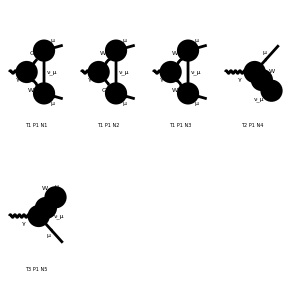

```mathematica
insW=DiagramSelect[ins1,!FreeQ[#,V[3]]&];
Paint[insW,PaintLevel->{Particles}];
```

```mathematica
ampW=CreateFeynAmp[insW,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

in total: 5 Particles amplitudes

```mathematica
resultW=CalcFeynAmp[ampW/.replacement]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-1/(π SW2)Alfa EL MM (1/4 Sub38 C0i[cc0,MM2,0,MM2,0,MW2,MW2]+(F3-F4) (Finite/8-1/4 B0i[bb0,MM2,0,MW2]-1/2 C0i[cc00,MM2,0,MM2,0,MW2,MW2]+1/2 MM2 (C0i[cc1,MM2,0,MM2,0,MW2,MW2]+C0i[cc2,MM2,0,MM2,0,MW2,MW2])))]

```mathematica
UVDivergentPart[resultW]//Simplify
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(3 Alfa Divergence EL (F3-F4) MM)/(8 π SW2)]

```mathematica
resultWList=calcFeynAmpList[ampW/.replacement]/.resultWList[[0]]->List;
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

```mathematica
uvDivW=Map[UVDivergentPart,resultWList]//Simplify
```

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][(3 Alfa Divergence EL (F3-F4) MM)/(8 π SW2)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0]]

```mathematica
uvDivWL=Map[#[[1]]&,uvDivW]/.uvDivW[[0]]->List
```

{0,0,(3 Alfa Divergence EL (F3-F4) MM)/(8 π SW2),0,0}